DateObject[]
"Sat 26 Feb 2022 19:08:14""GMT"+11

```mathematica
namesInitial = Names["Global`*"];
```

```mathematica
t0=AbsoluteTime[];
figNo=1;
captionStyle={FontFamily-> "Source Sans Pro", FontSize->16};
captionStyle={FontFamily-> "Book Antiqua", FontSize->16};
$Line=0;
```

Running Time: ~ 160,  190, 200, 163, 189, 197, 202 seconds.

# Chapter 49 | Supporting Notebook

## NOTE TO RB, Buttons

NOTE TO RB:
The following Buttons are only to make it easy for me to refer quickly to your source PDF while I’m doing screenshots from it into this notebook.
The file path inside the SystemOpen[] is of course quite specific to my system.
(They can obviously be dispensed with in the final version of this Supporting Notebook.)
Most yellow stuff is notes to you.
All the coloured background stuff should be removed eventually.

```mathematica
Print[Style[Button[ "Volume-4.1.pdf | (RB original).pdf",SystemOpen["/Users/macbook/Documents/BJSdata/aaa People/Blower, David J/VOLUME IV Project/Volume IV | PDFs and NBs (from Old Spud)/TeXShop/TeXShop | RB to BJS | Tue22Feb2022/Volume-4.18.pdf"](*, Appearance->"Pressed"*)],Background->Magenta]]
(If[$FrontEnd =!= $Failed, SelectionMove[EvaluationNotebook[], All, GeneratedCell];
     FrontEndTokenExecute["SelectionCloseUnselectedCells"]])
```

Volume-4.1.pdf | (RB original).pdf

```mathematica
Print[Style[Button[ "Volume-4.18 | Chapter 49.pdf",SystemOpen["/Users/macbook/Documents/BJSdata/aaa People/Blower, David J/VOLUME IV Project/Volume IV | PDFs and NBs (from Old Spud)/TeXShop/TeXShop | RB to BJS | Tue22Feb2022/Volume-4.18 | Chapter 49.pdf"](*, Appearance->"Pressed"*)],Background->Magenta]]
(If[$FrontEnd =!= $Failed, SelectionMove[EvaluationNotebook[], All, GeneratedCell];
     FrontEndTokenExecute["SelectionCloseUnselectedCells"]])
```

Volume-4.18 | Chapter 49.pdf

## Editors’ Notes

1.
Throughout this and the other Supporting Notebooks, we will have occasion to refer to the author of the Information Processing series. We feel on the one hand that repeatedly referring to our late friend as David is perhaps a little bit too personal in this context, but on the other hand referring to him as Blower seems all together too impersonal. Our compromise is to refer respectfully to the author of his unfinished volume IV as DB.

2.
In this and the other Supporting Notebooks, text—both English and Mathematica—quoted directly from Volume IV is indented in Times New Roman font, thus:

In this the other Supporting Notebooks, text—both English and Mathematica—quoted directly from Volume IV is indented in Times New Roman font, thus:

NOTE TO RB:
I propose that we do not use any coloured background in the final SN; This is just for our convenience as we develop the SNs.

4.
Numerical values produced by DB’s Mathematica ANN code and reported in his text will almost certainly never be exactly replicated by the same code in this Notebook. This is due to the different values of the system variable $RandomState at the moment of calculation in the respective computers involved.

## Introduction

In this Supporting Notebook for Chapter 49, Artificial Neural Networks and Probability, we provide working Mathematica code reflecting accurately as possible the code presented by David Blower in the text of his Chapter 49, Volume IV.

As discussed elsewhere, this Notebook and it’s companion Supporting Notebooks will make extensive use of the functions defined in the IP package, which therefore must be called first before the rest of the code in each Notebook will execute properly. If the following Needs[] statement executes properly, the full Notebook should execute without error in a running time of around 140-150 seconds.

## Installing and Checking the IP Package

In this Supporting Notebook fro Chapter 49 we include a fuller discussion and analysis of the IP package than we include in the Supporting Notebooks for Chapters 50, 51, 52, 53, and 54. We demonstrate such functions as functionListing[], functionCount[], and functionListInformation[].

In the other Supporting Notebooks we simply call Needs[“IP`”] and then functionListing[“IP`”].

If the package file IP.m has been correctly installed in the reader’s system (see the Notebook Read-Me-First.nb), the following Needs[“IP`”] statement will install the functions defined in the IP package.

```mathematica
Needs["IP`"]
```

Several of the functions in the IP package itself allow the reader to check that the functions have been installed properly. We illustrate the operation of these function only in this Section, Installing and Checking the IP Package, of this Supporting Notebook for Chapter 49, assuming that this is the first Supporting Notebook investigated by the reader. Only the preceding Needs[] statement is included at this point in the other Supporting Notebooks.

functionListing[] outputs an alphabetically sorted list of the names of all the Package functions. Here is its Usage statement.

```mathematica
?functionListing
```

This illustrates its intended function:

```mathematica
functionListing["IP`"]
```

{aF,appleColours,autoCollapse,basisEj,captionNeat,captionNeatFigured,cellName,cellNumberingAssociation,cellTable,cellTable2,cellValue,chap50MEP,codeInTextCell,conditionalStatements,constraintFunctionAveLambda,constraintFunctionAveMEP,constraintFunctionMatrix,constraintFunctionVectorF,entropy2,entropyH,entropyQiMEP,eta,expectationF,framedNoLabelWithCaption,functionCount,functionListInformation,functionListing,highlight,infoPrint,inputGivesOutput,interactionF,interactionF,kanga,kanga,klDivergence,lagrangeLambdaN,lagrangeMEP,lambda,laplaceRuleOfSuccession,marginalStatements,maxentQi,mepAlgorithm,mepAlgorithmProbabilities,metricTensorG,metricTensorMEP,myJoinImages,myMultinomial,mySymbolQ,myTextRecogniseCode,myTiming,myXlogX2,numberOfFrequencyCounts,numberOfFrequencyCounts,numberOfMicroStatements,numberOfPermutations,partitionFunctionMEP,partitionFunctionZ,pConditionalProbability,pProbability,probabilityConditionedOnModel,probabilityOfFutureFrequencyCounts,probabilityQi,probPlot,qConditionalProbability,qi,qLambda,qLambda,qProbability,qReplace,recoveredCode,reDistance,reprotectPlus,sizeOfSampleSpace,sizeOfSampleSpace,sizeOfSampleSpace,statementSymbol,statementVector,stateSpace,theta,twoAxisPlot,unprotectPlus,varType}

If the reader has started with a clean Mathematica kernel, there should be no defined functions in the Global ` context:

```mathematica
functionListing["Global`"]
```

{}

functionCount[] does just what you might expect:

```mathematica
?functionCount
```

```mathematica
functionCount["IP`"]
```

82

```mathematica
functionCount[]
```

0

At this point functionListInformation[] outputs the usage statements of all the Package-defined functions.

```mathematica
?functionListInformation
```

Noting that: “If a function does not have a usage statement, the function code will be listed”, this function was useful during the development of the Package, detecting defined functions without a Usage statement since the full code—no blue background—is listed rather than a usage statement. WRI strongly suggest that functions written for use in “public” Notebooks should have many of the properties and attributes of Mathematica’s own functions, including easily obtained online help.

```mathematica
(* ⌚ 23 seconds *)
functionListInformation["IP`"];
```

aF[cfv] returns a list of Symbol[]s of the form {aF1, aF2, …, aFn} corresponding to the n rows of the matrix of constraint function vectors cfv.

appleColours[] gives a list of colours defined for stylistic purposes and used through the Blower Notebook collection accompanying Volume IV.
These colour definitions are:
blue=RGBColor[24/100,43/100,62/100];
green=RGBColor[44/100,64/100,37/100];
yellow=RGBColor[93/100,68/100,33/100];
red=RGBColor[79/100,25/100,25/100];
purple=RGBColor[51/100,33/100,55/100];
grey=RGBColor[56/100,58/100,57/100];
brown=RGBColor[59/100,39/100,24/100];

autoCollapse[] called immediately after preceding code - often a call to Plot[] or similar, which may entail many lines of graphical control code of no direct imnterest to the subject matter - neatly folds away all the previous calling code, allowing a clean Notebook appearance.
A typical use of autoCollapse[] looks like:
*****
st = {FontFamily->''Garamond'', FontSize->16}
Plot[ codecodecodecodecodecodecode ];
Labeled[ %, Style [ StringForm[ ''Plot[Sin[x],{x,0,2π}]'' ],st ] ]//Print
autoCollapse[];
*****
This usage avoids the introduction of variables such as plt and lbplt.
The following //Print eliminates the output Cell label.

basisEj[cfm] gives a matrix of the same dimension as cfm, (e.g., r × c).
The c elements in the i^th row  are the Log[]s of the elements of the c symbolic  probabilities (where the Lagrange parameters are λ_i) given by probabilityQi[cfm], differentiated with respect to λ_i.
basisEj[] calls probabilityQi[] and lambda[].

captionNeat[captionString, lineLength] produces a version of the string captionString in which the text is presented in lines each having lineLength words, followed by any last line shorter than lineLength words.
Commas in the caption are specially treated; all other punctuation is accommodated.
An example shows how to incorporate non-black text.
Another example shows how to use captionNeat[] for the captions of Framed screenshots.

captionNeatFigured[captionString,charsPerLine] produces a String consisting of captionString prefixed by, e.g., ''Figure 17. '' extending when necessary over several lines.
The Figure number is automatically incremented. (figNo should be initialised Globally.)
The parameter charsPerLine governs (roughly) the number of characters per line.
Coloured words are not permitted.

cellName[joint,order] returns the cell name Q_n of the joint statement joint in the state space represented by the (Mathematica Symbol `nemo`) order.
cellName[] calls cellNumberingAssociation[] and statementSymbol[].

cellNumberingAssociation[order] returns an Association with the mapping
of the cell numbers xi to the joint statements in the state space. And vice versa. 
The numbering is consecutively from outside-to-inside. For example in A2B2C2, A is the outermost statement
and C is the innermost, or a nesting A[B[C]].
First the C statements are traversed, then the B statements, and then the A statements.
cellNumberingAssociation[] calls statementVector[] and statementSymbol[].

cellTable[order] returns a nested List of all joint statements in the state space (with their cell numbers).
 The Mathematica Symbol order (i.e., order has Head[] Symbol) is the ordering for the joint statements.
 The function MatrixForm[] is used for the rectangular display.
cellTable[] calls cellNumberingAssociation[] and stateSpace[].

cellTable2[order] returns the nested List of all joint statements cell numbers in the state space.
 The Mathematica Symbol `order` is the ordering for the joint statements.
 The function MatrixForm['] is used for the rectangular display.
cellTable2[] calls cellNumberingAssociation[].

cellValue[values] returns the cell numbering and values as ''number:value'' strings.
 The function MatrixForm[] is used for the rectangular display.

chap50MEP[cfm,cfa] returns the probabilities Q_i.
cfm is the matrix of constraint functions.
cfa is a vector of contsraint values.
chap50MEP[] calls lagrangeMEP[].

codeInTextCell[text1,code,text2] produces a Text cell consisting of:
(i) the text in text1, followed by …
(ii) the *result* of executing code, followed by …
(iii) the text in text2.
For example:
codeInTextCell[ ''We refer to Figure'', (figNo),  ''below.'' ]
⟹
We refer to Figure 15 below.
Note that if the reference is to a previous rather than a following Figure, we want:
codeInTextCell[ ''We refer to Figure'', (figNo-1),  ''above.'' ]
⟹
We refer to Figure 15 above.
(Typically the variable figNo is incremented via figNo++ when each Figure's caption is generated, so must be decremented if called after the immediately preceding Figure).
codeInTextCell[] calls autoCollapseInternal[] so that the code calling codeInTextCell[] is folded away.
Inspiration for this function came from the StackExchange page herehttps://mathematica.stackexchange.com/questions/211225/how-to-mix-text-and-formulas-in-a-single-cell-in-the-wolfram-cloud-notebookNonehttps://mathematica.stackexchange.com/questions/211225/how-to-mix-text-and-formulas-in-a-single-cell-in-the-wolfram-cloud-notebookHyperlinkActionRecycledHyperlinkActive.

conditionalStatements[stat,cond,nemo] returns two lists {l1,l2} which comprise the conditional joint statements of stat.
  The Lists l1 and l2 hold the joint statements of the numerator and the denominator, (See Blower Eq. 42.14)
  The Mathematica Symbol nemo is the Point Nemo for the state space.
conditionalStatements[] calls marginalStatements[].

constraintFunctionAveLambda[cfm, lambda] returns the constraint function averages
associated with the constraint function matrix cfm and the corresponding lambda values.

constraintFunctionAveMEP[cfm,qi] returns the constraint function averages
given by the product cfm.qi, where qi is a list of the probabilities Q_i.

constraintFunctionMatrix[order] generates a List[] of constraint function vectors based on the symbol order.
Although the function name contains the substring ''matrix'' the generated List[] is not mathematically a matrix, although it can be made to look like a matrix with MatrixForm[].
constraintFunctionMatrix[] calls statementVector[] and constraintFunctionVectorF[].

constraintFunctionVectorF[int,order] returns the constraint function vector for the interaction int (which can be a Symbol or an Integer), based on the state space based on order.
constraintFunctionVectorF[] calls interactionF[], marginalStatements[], cellNumberingAssociation[], and stateSpace[].

If arg is a List or Vector and consists of only numeric elements p_i and
∑ p_i == 1, entropy2[arg] returns the numerical entropy -∑ p_i ln(p_i).
If arg is a List or Vector and consists of only numeric elements p_i and ∑ p_i != 1, an error message is returned.
If arg is not a List or Vector an error message is returned.
If arg consists of only symbolic elements, the symbolic expression
-∑ p_i ln(p_i) is returned, e.g., ''-p1 Log[p1]-p2 Log[p2]''.
If arg consists of both numeric and symbolic elements, p_i Log(p_i) is calculated for the numeric elements, while a symbolic form such as ''p1 Log[p1]'' is returned for any symbolic elements.

entropyH[cfm] returns the symbolic (with the symbolic Lagrange multipliers represented as λ_i) entropy of the probabilities {Subscript[q, 1],Subscript[q, 2],...,Subscript[q, n]}, i.e., the entropy -∑ q_i Log(q_i).
The probabilities {Subscript[q, 1],Subscript[q, 2],...,Subscript[q, n]} are calculated using probabilityQi[cfm].
The q_i are non-negative and by construction add to 1.
entropyH[probList] returns the numerical entropy of the numerical probabilities (which must sum to 1) in the list probList.
entropyH[cfm] calls probabilityQi[cfm] only if the argument cfm is a Matrix.

entropyQiMEP[cfm,cfa] reurns the entropy of the probabilities Subscript[Q, i]
derived from the (numeric) constraint function matrix cfm and the associated (numeric) constraint function averages vector cfa.
entropyQiMEP[] calls chap50MEP[]

eta[cfm] returns a list of Symbol[]s of the form {η1, η2, …, ηn}
corresponding to the n rows of the cfm matrix; each of the n rows is a constraint function vector cfv.

expectationF[λ,cF] forms the matrix.vector product of the (r×c) matrix cF and the (c×1) vector maxentQi[λ,cF].
expectationF[] calls maxentQi[].

framedNoLabelWithCaption[g,caption,iSize] produces a Framed version of the graphic g, with ImageSize iSize (default 700), Print-ed so that there is no Cell Label.
g must be a graphic, usually a screenshot.
Below the Framed graphic the centred caption is rendered as ⌘-7 text.
Since a local definition of autoCollapse[] is included in framedNoCellLabel[]'s defining code, the final result is super clean, as the call to framedNoCellLabel[] is ''folded'' away and thus invisible.
Usage such as:

framedNoLabelWithCaption[ g, Style[ StringForm[StringJoin[  ''Figure `1`. '', captionNeat[ String, 12]],figNo++], captionStyle ],700 ]

will output a Framed-ed and caption-ed with:
(i) An automatically incrementing Figure number; and
(ii) the caption String produced by captionNeat[] in the (Globally defined) style captionStyle.
The second integer parameter to captionNeat[] is the required words-per-line, a mechanism designed to control the appearance of the caption text.

functionCount[context] gives a count of the symbols in the Context[] context that have nontrivial DownValues, i.e., all the user-defined functions in the Context[] context.
A nominated context - as in functionListInformation[''contextName`''] - must be the name of another Context[], i.e., whose last character is `.
functionCount[context] counts functions in the Context[] context that both do and do not have a usage statement.
The default context is ''Global`''.

functionListInformation[context] gives an alphabetic listing of all the Information[] for the symbols in the Context[] context that have nontrivial DownValues, i.e., all the user-defined functions in the Context[] context.
The default context is ''Global`''.
If a function does not have a usage statement, the function code will be listed.

functionListing[context] gives an alphabetic list of all the symbols in the Context[] context that have nontrivial DownValues, i.e., it gives a list of all the defined functions in the Context[] context.
functionListing[''IP`''] gives an alphabetic list of all the functions in the IP package.
Since the default context is ''Global`'', functionListing[] gives an alphabetic list of all the functions in the Global context. i.e., the ''locally'' defined functions.
functionListing[context] lists functions in the Context[] context that both do and do not have a usage statement.

highlight[cell,valCol] outputs the String cell (of the form, e.g., ''cellNumber:cellValue'') in the colour in the list valCol
(of the form, e.g.,  {{cellNumber, ''Red''},{cellNumber, ''Blue''},.…}) whose cellNumber matches the cellNumber in cell.
For example,
highlight''12:0.345'',{{''12'',Red},{''12'',Blue}}] ⟹ 12:0.345
whereas
highlight''11:0.345'',{{''12'',Red},{''11'',Blue}}] ⟹ 12:0.345.

infoPrint[string] is used to produce custom usage statements having italics and other font/face/size formatting combinations which do *not* adversely affect the ⌘-shift-K function  templating functionality.

inputGivesOutput[code] produces printed output of the form code ⟹ res, where res is the result of evaluating code.
If the input code is of the form var = code, the variable var is correctly assigned to the result of evaluating code.
Note that in such cases, to invoke inputGivesOutput[] using PostFix syntax, enclose the input code in parentheses:
(var = code) // inputGivesOutput.
The 2^nd last code line (''ToExpression[codeString];'')—before autoCollapse1[]—ensures that any following input using ''%'' to refers correctly to the output from code.
inputGivesOutput[] calls autoCollapseInternal[] ''internally''so that the calling Input is folded away.

interactionF[int,order] returns a Symbol for the interaction int, which can be a Symbol or an Integer.
interactionF[] calls statementVector[] and statementSymbol[].

kanga[traitList] returns the joint statement Symbol based on the individual traits in traitList.
The complete list of correspondences is:
{Smart→A1,Dumb→A2,Fosters→B1,Corona→B2,RH→C1,LH→C2,Sandy→D1,Beige→D2,Melbourne→E1,Sydney→E2}.
For example, kanga[{RH,Smart,Corona,Beige,Melbourne}] ⟹ A1B2C1D2E1.
kanga[sym] returns the List of traits; for example, kanga[A1B2C1D2E1] ⟹ {Smart,Corona,RH,Beige,Melbourne}.
kanga[] calls statementSymbol[].

klDivergence[dist,distRef] gives the Kullback-Leibler (KL) distance between the two discrete distributions dist and distRef.
The KL divergence or distance, D_KL (also called relative entropy), is a measure of how one probability distribution (dist) is different from a second, reference probability distribution (distRef).
(See also https://en.wikipedia.org/wiki/Kullback%E2%80%93Leibler_divergence).
Although it is often intuited as a way of measuring the distance between probability distributions, the Kullback–Leibler divergence is not a true metric; in general, klDivergence[d1,d2] != klDivergence[d2,d1].

lagrangeLambdaN[averageF,cF] gives the numerical values of the Lagrange multipliers found by setting the matrix.vector product of the (r×c) matrix cF and the (c×1) vector maxentQi[λ,cF] equal to the (r×1) vector of numerical constraint function averages averageF.
lagrangeLambdaN[] calls expectationF[] and NSolve[].

lagrangeMEP[cfm,cfa, wp] returns the Lagrange parameters Subscript[λ, j] with precision wp, whose default value is MachinePrecision.
cfm is the matrix of constraint functions.
cfa is a vector of constraint values.
lagrangeMEP[] calls NMinimize[], in which WorkingPrecision is set to 30.

lambda[cfm] returns a list of Symbol[]s of the form {λ1, λ2, …, λn}
corresponding to the n rows of the cfm matrix; each of the n rows is a constraint function vector cfv.

laplaceRuleOfSuccession[list] gives the probabilities (Subscript[N, i]+1)/(N+n), according the Laplace's Rule of Succession. The elements Subscript[N, i] in list are non-negative integers, with sum N, and n is the dimension of list.
This version of laplaceRuleOfSuccession[] also accepts symbolic input.

marginalStatements[stat,nemo] returns a list of joint statements which comprise the marginal sum of stat.
  The Mathematica Symbol nemo is the Point Nemo for the state space.
  marginalStatements[stat,nemo] returns an empty List {} when the joint statement stat is not in the state space nemo.
marginalStatements[] calls stateSpace[] and statementVector[].

maxentQi[λ,cF] gives a list of the (symbolic) probabilities Q_i corresponding to the (r×c) constraint function matrix (i.e., the matrix of constraint function vectors) cfm. 
The symbolic Lagrange multipliers are the indexed list of r symbols in the list λ. An example would be {α_1, α_2, α_3}.

mepAlgorithm[cm,cfa], given a List of constraint function averages (cfa) and a matrix (actually a list of lists of constraint function coedfficients masquerading as a matrix, cm), outputs a labelled list of its internal variables, both diagnostic and those of external interest, such as the Maximum Entropy probabilities (in real and rational forms), the corresponding entropy, the partition function (symbolic and numerical), and a ''check'' calculation of the input cfa.

mepAlgorithmProbabilities[cm, cfa],given a List of constraint function averages (cfa) and a matrix (actually a list of lists of constraint function coedfficients masquerading as a matrix, cm), outputs, a list of the Maximum Entropy probabilities (as reals).

metricTensorG[cfm] forms the natural log of the partition function of cfm and then calculates the symbolic matrix consisting of the partial derivatives of the second partition function with respect to the dummy variables λ1, λ2, …, .
There are as many λ's as there are rows in cfm.
metricTensorG[{{1,0}}] gives
(ⅇ^λ1/((1+ⅇ^λ1)^2)).
metricTensorG[{{1,0},{0,1}}] gives
(ⅇ^(λ1+λ2)/((ⅇ^λ1+ⅇ^λ2)^2) | -ⅇ^(λ1+λ2)/((ⅇ^λ1+ⅇ^λ2)^2)
-ⅇ^(λ1+λ2)/((ⅇ^λ1+ⅇ^λ2)^2) | ⅇ^(λ1+λ2)/((ⅇ^λ1+ⅇ^λ2)^2)).
metricTensorG[] calls partitionFunctionZ[] and lambda[].

metricTensorMEP[cfm,cfa] returns the metric tensor associated with
the constraint function matrix cfm and the constraint function averages cfa.
metricTensorMEP[] calls chap50MEP[].

myJoinImages[img1, img2] joins the (usually) screenshots img1 and img2 vertically to make a composite image whose width is the width of img1.
Useful for making a single (apparent) screenshot from two screenshots, from the bottom of page n and the top of page n+1 respectively.

myMultinomial[freq] gives a symbolic output if (all!) the elements of freq are symbolic, unlike the builtin function Multinomial[].

If Head[x] is Symbol or Subscript, mySymbolQ[x] returms True, otherwise False.

myTextRecogniseCode[codeScreensShot_] produces an executable Input (i.e., code) cell from the output of a call to TextRecognize[] with codeScreensShot - a screenshot of some text - as input.
codeScreensShot is displayed Framed, but as is.
TextRecognize[] is applied directly to codeScreensShot

When $Pre is set to myTiming, a report of the form ''wallclock execution time = t'' is printed in 12 point purple Arial font after each evaluation if the difference between AbsoluteTime[] before and AbsoluteTime[] after the evaluation is more than $TimeUnit (0.01 seconds).
If the wallclock execution time is greater than a minute and less than an hour the time is given in minutes and seconds.
If the time is greater than an hour the time is given in hours, minutes and seconds.
If the wallclock execution time is greater than a minute, the execution time in seconds is given in parentheses after the report in ''minutes and seconds'' or ''hours, minutes and seconds'' format.

myXlogX2[p] returns the numerical value of p Log[p] if NumberQ[p] is True, otherwise a symbolic expression such as ''p1 Log[p1]''.
If p=0 or p=0.0, 0 is returned.

numberOfFrequencyCounts[n,N] gives the total number of different frequency counts u of the expansion n^N = ∑_(j=1)^u W_j(N).
Here n the size of the state space and N the size of the sample space. 
numberOfFrequencyCounts[{Subscript[N, 1],Subscript[N, 2],...,Subscript[N, n]}] gives the number u from a single, representative contingency table.
1/u is the probability of a future frequency count in an uninformative state of knowledge.

numberOfMicroStatements[{N_1,N_2, …, N_n}] gives the Multinomial coefficient W(Subscript[N, 1],Subscript[N, 2],...,Subscript[N, n]), or multiplicity factor.
Symbolically, for example, numberOfMicroStatements[{a,b,c}] is ((a + b + c)!)/(a! b! c!).

numberOfPermutations[cont] gives the number of distinct permutations from a single representative contingency table cont.  
The total of all permutations of possible occupancy patterns {N,0,...,0}, {N-1,1,...,0}, {N-2,2,...,0}, etc. is the number given by numberOfFrequencyCounts[n,N].

partitionFunctionMEP[cfm,cfa] returns the value of the partition function 𝒵
based on the constraint function matrix cfm and the associated constraint function averages cfa.
partitionFunctionMEP[] calls lagrangeMEP[].

partitionFunctionZ[cvm] returns the sum ∑_(j = 1)^n Exp[λ_j.cfm], where n is the number of rows of cvm.
partitionFunctionZ[] calls lambda[].

pConditionalProbability[stat,cond,nemo] returns conditional probability of stat conditioned on cond, as the ratio of probability Symbols.
For example pConditionalProbability[C1,A1B1,A2B2C2] returns P[A1B1C1]/(P[A1B1C1] + P[A1B1C2]).
   The Mathematica Symbol nemo is the Point Nemo for the state space.
pConditionalProbability[] calls conditionalStatements[].

pProbability[stat,nemo] returns marginal probability of stat as the sum of probability Symbols, e.g. P[A1B1C1]+P[A1B1C2]. The Mathematica Symbol nemo is the Point Nemo for the state space.
pProbability[] calls marginalStatements[].

probabilityConditionedOnModel[freq,prob] gives the probability W(Subscript[N, 1],Subscript[N, 2], …, Subscript[N, n]) 
q_1^N_1 
q_2^N_2... q_n^N_n for counts freq, i.e., the N_i, and probabilities prob, i.e., the q_i, as specified under a model ℳ.
This is the PDF of the Multinomial distribution.

probabilityOfFutureFrequencyCounts[freq,alpha] gives the probability of observing the future frequency counts freq, i.e., {N_1,N_2, …,N_n}, assuming a Dirichlet distribution with parameters alpha, i.e.,
{α_1,α_2, …, α_n} for P(ℳ_k).

probabilityQi[cfm] returns a list of the (symbolic) probabilities Q_i
corresponding to the constraint function matrix (i.e., matrix of constraint function vectors) cfm. 
The symbolic Lagrange multipliers are represented as λ_i.
probabilityQi[] calls lambda[] and partitionFunctionZ[].

probPlot[{l_,u_},{params__},dist_] produces a (captioned) plot of the PDF of the distribution dist with parameters params, together with a shaded region under the PDF curve representing the integral from l to u.
Sensible l and u limits determine a sensible interval over which the PDF is plotted.
The numerical value of the integral is displayed beside the PDF curve, as is the distribution with its parameters.

qConditionalProbability[stat,cond,order] returns the conditional probability of stat conditioned on cond, as the ratio of Qi Symbols. For example qConditionalProbability[C1,A1B1,A2B2C2]  returns Q1/(Q1+Q2).
 The ordering of statements in order defines the cell numbers Qi.
qConditionalProbability[] calls conditionalStatements[] and cellNumberingAssociation[].

qi[cfm] returns a list of Symbol[]s of the form {Q1, Q2, …, Qn}
corresponding to the n rows of the cfm matrix; each of the n rows is a constraint function vector cfv.

qLambda[cfm, i] gives a list of subscripted λ symbols, e.g, {λ_1,λ_4,λ_7}, corresponding to the non-zero elements in the i^th column of cfm.

qProbability[stat,order] returns marginal probability of stat as the sum of Qi Symbols, e.g. {Q1+Q3}. 
The ordering of statements in order defines the cell numbers Qi.
qProbability[] calls marginalStatements[] and cellNumberingAssociation[].

qReplace[qi,subscript] creates a list of replacement rules {Q1->qi[[1]],Q2->qi[[2]],...} (default,subscript:False),
or with subscripted symbols {Q_1->qi[[1]],Q_2->qi[[2]],...} (subscript:True).

recoveredCode[functionName] produces an ''Input'' cell containing the code defining the (previously defined!) function functionName in either the ''IP`'' or ''Global`'' contexts.
The generated ''Input'' cell is *not* bracketed with the ''Input'' cell in which this function is called.
Selecting the cell bracket of the (one-line) generated ''Input'' cell and pressing ⌘-9 will convert the cell into a properly formatted ''Input'' cell, i.e., it will have appropriate line breaks and syntax colouring.

reDistance[dist,distRef] gives √(2\klDivergence[dist, distRef]).
reDistance[] calls klDivergence[].

reprotectPlus[] reverses the effect of unprotectPlus[].
After executing reprotectPlus[] an expression such as a-3 will (again) be output (unconventionally!) as -3+a.

sizeOfSampleSpace[n,M]  gives the numeric value of n^M, with n the size of the state space and M the number of samples.
sizeOfSampleSpace[{Subscript[a, 1],...,Subscript[a, n]},{Subscript[A, 1],...,Subscript[A, M]}] gives n^M, with the state space {Subscript[a, 1],...,Subscript[a, n]} and samples {Subscript[A, 1],...,Subscript[A, M]}.
This version of sizeOfSampleSpace[] also accept symbolic input.

statementSymbol[join] returns a Mathematica Symbol.
For instance, statementSymbol[{A3,B2,C1}] returns the symbol A3B2C1.
The symbols in the list join are concatenated (in alphabetical order) into a single Symbol.

statementVector[stat] returns a sorted List. For example statementVector[A3B2C1] is returned as {A3,B2,C1}. 
  The expression A3B2C1 is an elementary point in the State Space (Blower Ch. 13.2.1).
  The statement stat is a Mathematica Symbol, being the conjunction of one or more single letter-digit pairs.

stateSpace[nemo] returns a sorted List of all joint statements in the state space.
 The Mathematica Symbol nemo is the Point Nemo for the joint statements.
The elementary statements are sorted alphabetically.

theta[cfm] returns a list of Symbol[]s of the form {θ1, θ2, …, θn}
corresponding to the n rows of the cfm matrix; each of the n rows is a constraint function vector cfv.

twoAxisPlot[{f_,g_},{x_,x1_,x2_},opts:OptionsPattern[]] plots the functions f and g together over the interval from x1 to x2 but with different vertical axes.
Each plot is fully scaled, with the left FrameTicks relating to f (in the matching blue colour ColorData[1][1]) and the right FrameTicks relating to g (in the matching colour dark red ColorData[1][2]).
The PlotLegends are also in the matching colours.

unprotectPlus[] has the effect of altering the sequence in which the arguments of Plus[] appear.
Note that since the FullForm[] of an expression such as a-3 is Plus[-3,a], this change
affects subtractions in the same way, which is the real point of this code.
As an example, before ever executing reprotectPlus[], an expression such as a-3 will be output (unconventionally!) as -3+a.
After executing unprotectPlus[] the expression a-3 will be output (conventionally!) as a-3.
The complementary function reprotectPlus[] reverse the effect of unprotectPlus[].

varType[varName] gives:
(i)  ''function'' if varName is the name of a function;
(ii) ''variable'' if varName is the name of a variable; and 
(iii) ''dummy variable'' if varName is a dummy or an as-yet-unassigned variable.

## Artificial Neural Networks and Probability: Motivation

As noted in our Editor’s Apologia, DB included two Chapters in Volume III introducing Artificial Neural Networks (ANNs) into his treatment of Information Processing. These were Chapter 42 Boltzmann Machines, and Chapter 43 Hidden Units for Boltzmann Machines.

At the beginning of Chapter 42 DB introduces Boltzmann Machines as follows:

Boltzmann machines provide us with an opportunity to discuss how certain general inferential problems often have unique, traditional, and perhaps, to some extent, accidental histories attached to them. These kind of contingent histories are quite understandable whenever a problem has been studied on its own merits over a long period of time.
	The topic of artificial neural networks (ANNs) presents us with one such class of inferential problems which have experienced a unique history. At first glance, ANNs appear to be somewhat detached from the conceptual underpinnings and the jargon that I have tried to associate with inference as a generalization of logic. Swimming against the tide, I would like instead to emphasize the commonalities shared by all inferential problems rather than their differences due to some particular contingent and accidental history.

The Introduction to Chapter 43 begins:

Let’s return to the theme of some contingent history associated with artificial neural networks. A by–product of such an accidental history is a certain idiosyncratic way of thinking about problems, together with an associated terminology and notation. I am going to couch the discussion in this Chapter by employing the Boltzmann machine’s own unique Gestalt as it formed outside of the separate and distinct contingent history that gave rise to general inferencing.
	Thus, this Chapter will tend to frame inferential explanations in terms of some neural network architecture, consisting of input units, hidden units, and output units. The input units and output units are labeled as visible units because they correspond to known observables in the real world, while the hidden units are latent variables created for the sole purpose of revealing some hidden pattern or structure not readily perceivable in the input units. The hidden units and output units are activated through weights connecting the units.
	The input units are activated when environmental variables are clamped to the input units, which then in turn feed into activation of hidden units, and finally into the activation of output units. These output units are supposed to represent any target variables. This propagation is an asynchronous dynamic affair with each activation a momentary fleeting thing awaiting the next round of new activations. All of the weights connecting two units undergo a continuous change that depends on a gradient.
The main question here is the following: Will the introduction of hidden units help the Boltzmann machine overcome the impediment of relying on models with information solely from double interactions?

We let these two quotations from Chapters 42 and 43 respectively stand as some motivation for the whole of Volume IV, and proceed to implement and in some cases Expand on the Mathematica  code included in Chapter 49.

```mathematica
$Line=0;
```

## 49.1 Introduction

No Mathematica  code.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 1.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 1. Screenshot from Volume IV, page 1.

## 49.2 Review of the Probabilistic Solution

No Mathematica  code.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.1 from Volume IV, page 3.", 112  ],figNo++], captionStyle ],500 ]
```

-Graphics-
Figure 2. Figure 49.1 from Volume IV, page 3.

This call to cellTable[] does NOT produce a table that agrees with DB’s Figure 49.1:

```mathematica
cellTable[A2B2]
```

(1:A1B1 | 2:A1B2
3:A2B1 | 4:A2B2)

```mathematica
?cellTable
```

This call to xxxx[] DOES agree with DB’s Figure 49.1:

```mathematica
cellTable2[A2B2]
```

From cellTable2: output given by: MatrixForm[Transpose[cell],TableDirections→{tableDirections}]

(1:A1B1 | 3:A2B1
2:A1B2 | 4:A2B2)

Note to RB:
Can we remove this diagnostic?

```mathematica
?cellTable2
```

This call to cellValue[] returns the probabilities in the appropriate cells.

```mathematica
cellValue[{{1/3,1/3},{0,1/3}}]
```

(1:1/3 | 2:1/3
3:0 | 4:1/3)

```mathematica
?cellValue
```

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, Chapter 49, page 6.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 3. Screenshot from Volume IV, Chapter 49, page 6.

```mathematica
cfm49=
{
   {1,0,1,0}   (* cells 1 and 3 for A is true *)
      ,{1,1,0,0}   (* cells 1 and 2 for B is True *)
      ,{1,0,0,0}   (* cell 1 for AB is True *) 
}; 
MatrixForm[%]
```

(1 | 0 | 1 | 0
1 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}.cfm49
```

{λ_1+λ_2+λ_3,λ_2,λ_1,0}

These are the constraint function averages (cfa):

```mathematica
cfa49={1/3,2/3,1/3}
```

{1/3,2/3,1/3}

```mathematica
?lagrangeMEP
```

These are the Lagrange parameters:

```mathematica
lagrangeMEP[cfm49,cfa49]
```

{-32.483020756207,0,32.483020756207}

```mathematica
?chap50MEP
```

These are the probabilities:

```mathematica
qi49=chap50MEP[cfm49,cfa49]
qi49//Chop//Rationalize
```

{0.333333,0.333333,2.60425×10^-15,0.333333}

{1/3,1/3,0,1/3}

```mathematica
?constraintFunctionAveMEP
```

These are the constraint function averages:

```mathematica
constraintFunctionAveMEP[cfm49,qi49]
%//Rationalize
```

{0.333333,0.666667,0.333333}

{1/3,2/3,1/3}

These should also return the constraint function averages:

```mathematica
cfm49.qi49
%//Rationalize
```

{0.333333,0.666667,0.333333}

{1/3,2/3,1/3}

```mathematica
?partitionFunctionMEP
```

This is the partition function value :

```mathematica
partitionFunctionMEP[cfm49,cfa49]
%//Rationalize
```

3.

3

## 49.3 The Multilayer Perceptron

No Mathematica  code.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 7.", 112  ],figNo++], captionStyle ],400 ]
```

-Graphics-
Figure 4. Figure 49.2 from Volume IV, page 7.

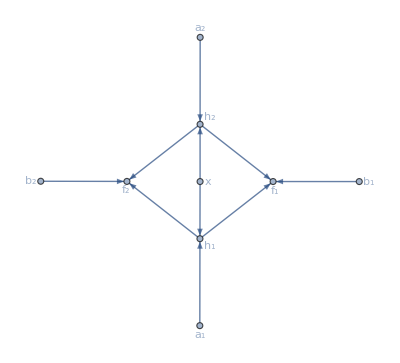
-Graphics-Figure 5 . The structure of the multilayer perceptron 
 in Figure 49.2 rendered by Graph[] with
GraphLayout -> ''SpringElectricalEmbedding''.

```mathematica
lineNumber=$Line;

a1=.
a2=.
Graph[
{x->Subscript[h, 1],Subscript[a, 1]->Subscript[h, 1]
  ,x->Subscript[h, 2],Subscript[a, 2]->Subscript[h, 2]
  ,Subscript[h, 1]->Subscript[f, 1],Subscript[b, 1]->Subscript[f, 1],Subscript[h, 2]->Subscript[f, 1]
  ,Subscript[h, 1]->Subscript[f, 2],Subscript[h, 2]->Subscript[f, 2],Subscript[b, 2]->Subscript[f, 2]
},
VertexLabels->Automatic,
GraphLayout->"SpringElectricalEmbedding"]//Framed;

Labeled[ %, Style[ StringForm["Figure `1` . The structure of the multilayer perceptron \n in Figure 49.2 rendered by Graph[] with\nGraphLayout -> ''SpringElectricalEmbedding''.",figNo++], captionStyle ] ]//Print

$Line=lineNumber-2;
autoCollapse[]
```

## 49.4 Mathematica Approach to a Solution for the Multilayer Perceptron

No Mathematica  code.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 8.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 6. Figure 49.2 from Volume IV, page 8.

### 49.4.1 Define the architecture

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 9.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 7. Figure 49.2 from Volume IV, page 9.

```mathematica
net=NetChain[{LinearLayer[2],ElementwiseLayer[Tanh],LinearLayer[2],SoftmaxLayer[]}
  ,"Input"->1
  ,"Output"->2
  ]
```

NetChain[<>]

(Click the “+“ sign in the preceding output to see the full structure of net.)

There are several ways to display the structure of the neural net, net.

Click the “+“ sign and either of the -Graphics- and  -Graphics- icons in the following output to see the full structure of net.

```mathematica
NetGraph[net]
```

NetGraph[<>]

Information about the structure of the network can be obtained in various ways; here are a few examples:

```mathematica
Information[net]
```

Net Information

```mathematica
net//Normal
```

{LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>],SoftmaxLayer[<>]}

This last output can be displayed as …

```mathematica
Column[net//Normal//Reverse]//Framed
autoCollapse[]
```

SoftmaxLayer[<>]
LinearLayer[<>]
ElementwiseLayer[<>]
LinearLayer[<>]

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 9.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 8. Figure 49.2 from Volume IV, page 9.

```mathematica
net = NetChain[{LinearLayer[2],ElementwiseLayer[Tanh],LinearLayer[2],SoftmaxLayer[]}
  ,"Input"->"Scalar"
  ,"Output"->2
  ]
```

NetChain[<>]

```mathematica
Column[%//Normal//Reverse]//Framed
autoCollapse[]
```

SoftmaxLayer[<>]
LinearLayer[<>]
ElementwiseLayer[<>]
LinearLayer[<>]

Again, clicking on the “+“ signs in the preceding output shows the full structure of net, with the input layer at  the bottom and the output layer at the top of the diagram.

### 49.4.2 Train the defined network

DB could have explained the following training data in slightly more detail by adding that training the network that if B is FALSE then P(A) = 0 requires training it so that the input vector {2} for B is associated with the output vector {0,1}, since the output vector is {P(A),P(Ā)}.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 10.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 9. Screenshot from Volume IV, page 10.

```mathematica
(* ⌚ ~20 seconds *)
trained=.
trained=NetTrain[net,{1->{0.5,0.5},1->{0.5,0.5},2->{0,1},2->{0,1}}
  ,LossFunction->CrossEntropyLossLayer["Probabilities"]
]
```

NetChain[<>]

trained =.
trained = NetTrain[net, {{1} -> {0.5, 0.5}, {1} -> {0.5, 0.5}, {2} -> {1, 0}, {2} -> {1, 0}}
    , LossFunction -> CrossEntropyLossLayer["Probabilities"]
  ]

Again, clicking on the “+“ signs in this output shows the full structure of net.

```mathematica
NetGraph[trained]
```

NetGraph[<>]

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 10.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 10. Screenshot from Volume IV, page 10.

RB:
Should  P (Ā | B = 1) be  P (A | B = 2) in Figure 8? And consequently, shouldn’t DB’s reported output for trained[2] be something like {~0, ~1}? , as in …

```mathematica
trained[1]
Log10[ trained[1] ]
```

{0.499935,0.500065}

{-0.301086,-0.300974}

```mathematica
trained[2]
Log10[ trained[2] ]
```

{0.000124866,0.999875}

{-3.90355,-0.0000542345}

```mathematica
trained[{3}]
```

{{0.0000256518,0.999974}}

```mathematica
trained[{0}]
Log10[ trained[{0}] ]
```

{{0.998656,0.0013444}}

{{-0.000584251,-2.87147}}

After all, in DB’s Figure 49.2 (our Figure 4), B (or not B) is the input to the network, and thus is the conditioning statement!?

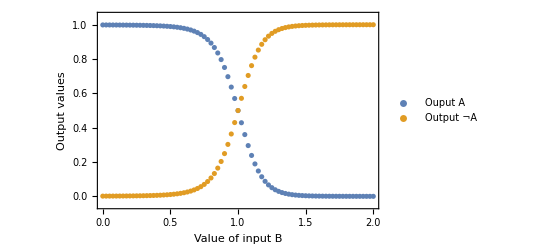
-Graphics-Figure 11. This shows the output from ''trained'' given only 2 instances
of {1}→{0.5,0.5} and 2 instances of {2}→{0,1}. The truth function
effectively synthesised by the network ''extrapolates'' to smaller
values of the input in an obvious way.

```mathematica
lineNumber=$Line;

ListPlot[ {Map[ (s↦{s, trained[s]⟦1⟧}), Table[in,{in, 0, 2, 0.025}] ],Map[ (s↦{s, trained[s]⟦2⟧}), Table[in,{in, 0, 2, 0.025}] ]}, ImageSize->400,PlotRange->{-0.05, 1.05},Frame->True, FrameLabel->{"Value of input B","Output values"}, PlotLegends->{"Ouput A","Output ¬A"}]//Framed;

Labeled[ %, Style[ StringForm[captionNeatFigured[ "This shows the output from ''trained'' given only 2 instances of {1}→{0.5,0.5} and 2 instances of {2}→{0,1}. The truth function effectively synthesised by the network ''extrapolates'' to smaller values of the input in an obvious way.", 70  ],figNo++], captionStyle ] ]//Print

$Line=lineNumber-2;
autoCollapse[]
```

We insert here an illustration of the effect of more training data; now the network is trained with 100 instances of B being TRUE and 100 instances of B being FALSE.

```mathematica
(* ⌚ ~40 seconds *)
trained=.
trained=NetTrain[net,
Table[ 1->{0.5,0.5}, 100 ]~Join~Table[ 2->{0,1}, 100 ]
  ,LossFunction->CrossEntropyLossLayer["Probabilities"]
]
```

NetChain[<>]

The reproduction of the training probabilities is now even more faithful.

```mathematica
trained[1]
Log10[ trained[1] ]
```

{0.499999,0.500001}

{-0.301031,-0.301029}

```mathematica
trained[2]
Log10[ trained[2] ]
```

{7.45295×10^-7,0.999999}

{-6.12767,-3.36518×10^-7}

```mathematica
trained[{3}]
```

{{1.27997×10^-7,1.}}

```mathematica
trained[{0}]
Log10[ trained[{0}] ]
```

{{0.999954,0.0000464928}}

{{-0.0000201915,-4.33261}}

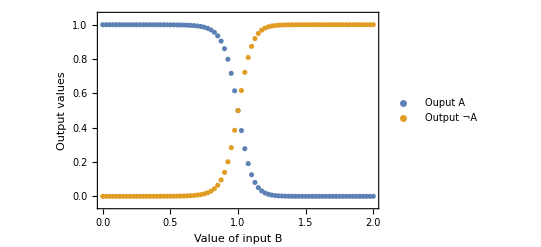
-Graphics-Figure 12. This shows the output from ''trained'' given 200 samples,
with 100 instances of {1}→{0.5,0.5} and 100 instances of {2}→{0,1}.
The truth function again effectively synthesised by the network
''extrapolates'' to smaller values of the input in an obvious way.

```mathematica
lineNumber=$Line;

ListPlot[ {Map[ (s↦{s, trained[s]⟦1⟧}), Table[in,{in, 0, 2, 0.025}] ],Map[ (s↦{s, trained[s]⟦2⟧}), Table[in,{in, 0, 2, 0.025}] ]}, ImageSize->400,PlotRange->{-0.05, 1.05},Frame->True, FrameLabel->{"Value of input B","Output values"}, PlotLegends->{"Ouput A","Output ¬A"}]//Framed;

Labeled[ %, Style[ StringForm[captionNeatFigured[ "This shows the output from ''trained'' given 200 samples, with 100 instances of {1}→{0.5,0.5} and 100 instances of {2}→{0,1}. The truth function again effectively synthesised by the network ''extrapolates'' to smaller values of the input in an obvious way.", 70  ],figNo++], captionStyle ] ]//Print

$Line=lineNumber-2;
autoCollapse[]
```

### 49.4.3 Shorter version

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 10.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 13. Screenshot from Volume IV, page 10.

```mathematica
net2 = NetChain[{2, Tanh, 2, SoftmaxLayer[ ]}, "Input"->"Scalar"]
```

NetChain[<>]

### 49.4.4 Longer version (Use of Association)

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 10.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 14. Screenshot from Volume IV, page 10.

```mathematica
(* Note that in this code, DB uses ""Input"→1 rather than "Input"→Scalar *)
net3=NetInitialize@NetChain[<|
        "layer1"->LinearLayer[2]
       ,"layer2"->ElementwiseLayer[Tanh]
       ,"layer3"->LinearLayer[2]
       ,"layer4"->SoftmaxLayer[]|>
       ,"Input"->1
       ,"Output"->2
]
```

NetChain[<>]

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 11.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 15. Screenshot from Volume IV, page 11.

```mathematica
(* ⌚ ~20 seconds *)
(* note now the form of the training data: {1}->{0.5,0.5}, rather than 1->{0.5,0.5} *)
trained3=NetTrain[net3,{{1}->{0.5,0.5},{1}->{0.5,0.5},{2}->{0,1},{2}->{0,1}}
  ,LossFunction->CrossEntropyLossLayer["Probabilities"]
]
```

NetChain[<>]

RB:
Learned a trick here. Can’t have arrows with hyperlinks to tagged cells in code. Trick is, enclose them within a
(* comment *).

```mathematica
trained3[{1}]
trained3[{2}] (*  ↓from500068  ↓from500068#2 *)
```

{0.499868,0.500132}

{0.00020142,0.999799}

Our output here is inconsistent with DB’s “trained3[{2}] giving {0.0077, 0.9923}”, as quoted immediately above.

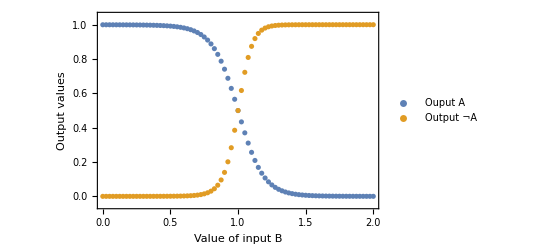
-Graphics-Figure 16. This shows the output from ''trained3'' given 2 instances
of {1}→{0.5,0.5} and 2 instances of {2}→{0,1}. The truth function
effectively synthesised by the network ''extrapolates'' to smaller values
of the input in an obvious way.

```mathematica
lineNumber=$Line;

ListPlot[ {Map[ (s↦{s, trained3[s]⟦1⟧}), Table[in,{in, 0, 2, 0.025}] ],Map[ (s↦{s, trained[s]⟦2⟧}), Table[in,{in, 0, 2, 0.025}] ]}, ImageSize->400,PlotRange->{-0.05, 1.05},Frame->True, FrameLabel->{"Value of input B","Output values"}, PlotLegends->{"Ouput A","Output ¬A"}]//Framed;

Labeled[ %, Style[ StringForm[captionNeatFigured[ "This shows the output from ''trained3'' given 2 instances of {1}→{0.5,0.5} and 2 instances of {2}→{0,1}. The truth function effectively synthesised by the network ''extrapolates'' to smaller values of the input in an obvious way.", 70  ],figNo++], captionStyle ] ]//Print

$Line=lineNumber-2;
autoCollapse[]
```

NetExtract[] can retrieve the Biases and Weights from a trained network:

```mathematica
Normal @ NetExtract[trained3,{"layer1","Biases"}]
Normal @ NetExtract[trained3,{"layer1","Weights"}]
```

{-0.570052,1.19264}

{{0.734752},{-1.07296}}

These values are rather different from DB’s values (p. 14)

Third layer : {b_1,b_2} and {{v_11,v_21},{v_12,v_22}}   (Note the unusual order of the indices.)

```mathematica
Normal@NetExtract[trained3,{"layer3","Biases"}]
Normal@NetExtract[trained3,{"layer3","Weights"}]
```

{-0.0943438,0.0943442}

{{-1.68096,3.69654},{2.44756,-3.54115}}

```mathematica
Transpose@Normal@NetExtract[trained3,{"layer1","Weights"}]
```

{{0.734752,-1.07296}}

Input True=1 and False=2 into the first layer:

```mathematica
(* True = 1 *)
Dot[{1},Transpose@Normal@NetExtract[trained3,{"layer1","Weights"}]]
(* False = 2 *)
Dot[{2},Transpose@Normal@NetExtract[trained3,{"layer1","Weights"}]]
```

{0.734752,-1.07296}

{1.4695,-2.14593}

### 49.4.5 Relationship to MEP

No Mathematica  code.

## 49.5 Connections to the Literature

No Mathematica  code.

## 49.6 Solved Exercises for Chapter Forty Nine

### Exercise 49.6.1: Write out the full expansion of the functions at the two output nodes.

No Mathematica  code.

It will be convenient to have DB’s sketch of a multilayer perceptron.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Figure 49.2 from Volume IV, page 7.", 112  ],figNo++], captionStyle ],400 ]
```

-Graphics-
Figure 17. Figure 49.2 from Volume IV, page 7.

The solution to Exercise 49.6.1 begins:

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 13.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 18. Screenshot from Chapter 49, page 13.

Then follows:

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 13.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 19. Screenshot from Chapter 49, page 13.

Here we bring forward some calculations from the “next exercise”, so as to be able the check the calculations fro Exercise 49.5.1.

```mathematica
{a1,a2}=Normal@NetExtract[trained3,{"layer1","Biases"}]  
{{u11},{u12}}=Normal@NetExtract[trained3,{"layer1","Weights"}]
```

{-0.570052,1.19264}

{{0.734752},{-1.07296}}

Linear equations in layer 1:

```mathematica
{u11*x+a1,u12*x+a2}/.x->1
{u11*x+a1,u12*x+a2}/.x->2
```

{0.1647,0.119673}

{0.899452,-0.953291}

Tanh[] function in layer 2:

```mathematica
Tanh[{u11*x+a1,u12*x+a2}/.x->1]
Tanh[{u11*x+a1,u12*x+a2}/.x->2]
```

{0.163227,0.119105}

{0.716031,-0.741269}

Combine the functions in h_1 and h_2:

```mathematica
ClearAll[h1,h2]

h1[x_]:=Tanh[u11*x+a1]  (* hidden node 1 *)
h2[x_]:=Tanh[u12*x+a2]  (* hidden node 2 *)

{h1[1],h2[1]}  (* True *)
{h1[2],h2[2]}      (* False *)
```

{0.163227,0.119105}

{0.716031,-0.741269}

Layer 3 : {b_1,b_2} and {{v_11,v_12},{v_21,v_22}}. (Note the extra Normal[] function extracting numerical values.)

```mathematica
{b1,b2}=Normal@NetExtract[trained3,{"layer3","Biases"}]
{{v11,v12},{v21,v22}}=Transpose@Normal@NetExtract[trained3,{"layer3","Weights"}]
```

{-0.0943438,0.0943442}

{{-1.68096,2.44756},{3.69654,-3.54115}}

The full functions:

```mathematica
ClearAll[f1,f2]

f1[x_]:=b1+v11*h1[x]+v21*h2[x]
f2[x_]:=b2+v12*h1[x]+v22*h2[x]

(* True *)
{f1[1],f2[1]} 
(* False *){f1[2],f2[2]}
```

{0.0715552,0.072082}

{-4.0381,4.47181}

Finally, Layer 4: the Softmax[] layer using the Exp[], gives (and see below) …

```mathematica
Exp[{f1[1],f2[1]}]/Total@Exp[{f1[1],f2[1]}]
Exp[{f1[2],f2[2]}]/Total@Exp[{f1[2],f2[2]}]
```

{0.499868,0.500132}

{0.00020142,0.999799}

Note that these last two lists of probabilities correspond to these.

The following Inputs set out the detailed calculations behind inputs such as trained3[{1}] and trained3[{2}]:

```mathematica
ClearAll[output]
output[input_]:= 
  Exp[
    Dot[
      Tanh[
        Dot[{input},Transpose@Normal@NetExtract[trained3, {"layer1", "Weights"}]] 
        + Normal@NetExtract[trained3, {"layer1", "Biases"}]
      ]
      ,Transpose@Normal@NetExtract[trained3, {"layer3", "Weights"}] ]
    + Normal@NetExtract[trained3, {"layer3", "Biases"}]
  ]
```

```mathematica
output[1]
output[2]
```

{1.07418,1.07474}

{0.0176309,87.5153}

After normalization we get

```mathematica
{output[1][[1]] / (output[1][[1]] + output[1][[2]])
,output[1][[2]] / (output[1][[1]] + output[1][[2]])}
```

{0.499868,0.500132}

```mathematica
{output[2][[1]] / (output[2][[1]] + output[2][[2]])
,output[2][[2]] / (output[2][[1]] + output[2][[2]])}
```

{0.00020142,0.999799}

Compare these values with the earlier results from trained3[]:

```mathematica
trained3[{1}]
trained3[{2}]
```

{0.499868,0.500132}

{0.00020142,0.999799}

This is satisfactory agreement.

### Exercise 49.6.2: Confirm the numerical values for the probability at the two output nodes of the first simple multilayer perceptron through independent Mathematica calculations.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 14.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 20. Screenshot from Chapter 49, page 14.

It is convenient to assign some variables to the results of these calculations:

```mathematica
{a1,a2}=Normal@NetExtract[trained3,{"layer1","Biases"}]
```

{-0.570052,1.19264}

```mathematica
{{u11},{u12}} = Normal@NetExtract[trained3,{"layer1","Weights"}]
```

{{0.734752},{-1.07296}}

The  Explicit calculations corresponding to Exercise 49.5.1 are …

```mathematica
Tanh[ a1 + u11 × 1 ]
```

0.163227

… and …

```mathematica
Tanh[ a2 + u12 × 1 ]
```

0.119105

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 15.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 21. Screenshot from Chapter 49, page 15.

```mathematica
Tanh[Dot[{1},Transpose[Normal@NetExtract[trained3,{"layer1","Weights"}]]]+Normal@NetExtract[trained3,{"layer1","Biases"}]]
```

{0.163227,0.119105}

Or …

```mathematica
Tanh[Dot[{1},Transpose[{{u11},{u12}}]]+{a1,a2}]
```

{0.163227,0.119105}

(Note that these are the two values calculated above via Tanh[a1+u11×1]and Tanh[a2+u12×1] respectively.)

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 15.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 22. Screenshot from Chapter 49, page 15.

```mathematica
Normal@NetExtract[trained3, {"layer3", "Biases"}]
```

{-0.0943438,0.0943442}

```mathematica
Normal@NetExtract[trained3, {"layer3", "Weights"}]
```

{{-1.68096,3.69654},{2.44756,-3.54115}}

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 15.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 23. Screenshot from Chapter 49, page 15.

```mathematica
Dot[ Tanh[Dot[{1},Transpose[Normal@NetExtract[trained3,{"layer1","Weights"}]]]+Normal@NetExtract[trained3,{"layer1","Biases"}]],
  Transpose[Normal@NetExtract[trained3, {"layer3", "Weights"}] ] +
  Normal@NetExtract[trained3, {"layer3", "Biases"}] ]
```

{0.161736,-0.0264247}

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 15.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 24. Screenshot from Chapter 49, page 15.

```mathematica
output[input_ ] := Exp[ Dot[ Tanh[ Dot[{input}, Transpose[Normal@NetExtract[trained3, {"layer1", "Weights"}]] ] +
      Normal@NetExtract[trained3, {"layer1", "Biases"}] ], Transpose[Normal@NetExtract[trained3, {"layer3", "Weights"}]] ] +
   Normal@NetExtract[trained3, {"layer3", "Biases"}] ]
```

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 25. Screenshot from Chapter 49, page 16.

```mathematica
output[1][[1]] / Total[output[1]]
```

0.499868

```mathematica
output[2][[1]] / Total[output[2]]
```

0.00020142

Recall from above …

```mathematica
trained3[{1}]
```

{0.499868,0.500132}

… and …

```mathematica
trained3[{2}]
```

{0.00020142,0.999799}

… or more completely …

```mathematica
{output[1][[1]] / Total[output[1]],output[1][[2]] / Total[output[1]]}
```

{0.499868,0.500132}

… and …

```mathematica
{output[2][[1]] / Total[output[2]],output[2][[2]] / Total[output[2]]}
```

{0.00020142,0.999799}

Again, these last two lists of probabilities agree with those here.

### Exercise 49.6.3: Show the explicit calculations being conducted at the SoftmaxLayer[ ] when viewed through the lens of the MEP formula.

No Mathematica  code.

We note that SoftmaxLayer[] must be computing a conditional probability P (A | B, ℳ_k), not a joint probability P (A, B | ℳ_k). However, the Q_i produced via the MEP formula are numerical assignments to joint probabilities.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 26. Screenshot from Chapter 49, page 16.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 27. Screenshot from Chapter 49, page 16.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 28. Screenshot from Chapter 49, page 16.

The data {{1}→ {.5, .5}, {{1}→ {.5, .5}, {{2}→ {0, 1}, {{2}→ {0, 1}} are simulating the set of equations (actually twice):

P(A_1|B_1)=(P(A_1,B_1))/(P(B_1))=Q_1/(Q_1+Q_2)=0.5
P(A_2|B_1)=(P(A_2,B_1))/(P(B_1))=Q_2/(Q_1+Q_2)=0.5
P(A_1|B_2)=(P(A_1,B_2))/(P(B_2))=Q_3/(Q_3+Q_4)=0
P(A_2|B_2)=(P(A_2,B_2))/(P(B_2))=Q_4/(Q_3+Q_4)=1

From this we immediately see that Q_3=0, and we are left with

Q_1+Q_2+Q_4=1

We have an underdetermined set of equations, for which we can obtain the range of allowed values via Reduce[]:

```mathematica
Reduce[
  {q1/(q1+q2)==1/2
     ,q2/(q1+q2)==1/2
,q3/(q3+q4)==0
,q4/(q3+q4)==1
     ,q1+q2+q3+q4==1
     ,0≤q1≤1
     ,0≤q2≤1
,0≤q3≤1
     ,0≤q4≤1
  }
  ,
  {q1,q2,q3,q4}
  ,Reals
]
```

0<q1<1/2&&q2==q1&&q3==0&&q4==1-q1-q2

By invoking the MEP as an extra principle, we can obtain a unique solution to this set of equations. Since q3==0, we need only solve for q1, q2, and q4. (This observation helps us avoids the troublesome evaluation of 0 Log[0].)

```mathematica
Maximize[
  {-q1 Log[q1]-q2 Log[q2]-q4 Log[q4]  (* entropy *)
  ,0<q1<1/2&&q2==q1&&q4==1-q1-q2 (* conditions *)
  }
  ,
  {q1,q2,q4}
]
```

{Log[3],{q1→q2,q2→1/3,q4→1/3}}

Note that the full solution  {1/3, 1/3, 0, 1/3}, including the q3=0, agrees with the “Implies” model A→B.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 29. Screenshot from Chapter 49, page 16.

We copy the reported numerical values from page 13:

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 13.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 30. Screenshot from Chapter 49, page 13.

```mathematica
{a1,a2}={1.84612,0.02466};
{u11,u12}={−1.47458,−0.60991};
```

```mathematica
{h1[x],h2[x]}
{h1[1],h2[1]}
```

{Tanh[1.84612-1.47458 x],Tanh[0.02466-0.60991 x]}

{0.355338,-0.526471}

Copying the reported numerical values from page 14:

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 14.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 31. Screenshot from Chapter 49, page 14.

```mathematica
{b1,b2}={−0.492303,0.492303};
{{v11,v12},{v21,v22}}={{1.73319,−2.22651},{0.75311,−0.08658}};
```

```mathematica
{f1[x],f2[x]}
{f1[1],f2[1]}
```

{-0.492303+1.73319 Tanh[1.84612-1.47458 x]+0.75311 Tanh[0.02466-0.60991 x],0.492303-2.22651 Tanh[1.84612-1.47458 x]-0.08658 Tanh[0.02466-0.60991 x]}

{-0.272925,-0.253279}

Opening the calculation of f1[1] to full scrutiny, we have:

```mathematica
f1[x]
```

-0.492303+1.73319 Tanh[1.84612-1.47458 x]+0.75311 Tanh[0.02466-0.60991 x]

```mathematica
Tanh[1.84612-1.47458 1]
```

0.355338

```mathematica
Tanh[0.02466-0.60991 1]
```

-0.526471

```mathematica
-0.492303+1.73319 Tanh[1.84612-1.47458 1]+0.75311 Tanh[0.02466-0.60991 1]
```

-0.272925

Note that entering numerical values into Mathematica typed exactly as they appear in a printed text gives values whose Precision is only what is “visible”:

```mathematica
{Rationalize[b1,0], Rationalize[b2,0]}
```

{-492303/1000000,492303/1000000}

Compare this “rational equivalent” calculation:

```mathematica
Exp[5.0]/1000
```

0.148413

Behind the displayed 6 significant figures there is a number with more precision:

```mathematica
Exp[5.]/1000//FullForm
```

0.148413

Thus Exp[5.0]/1000 is not equal to 148413/1000000…

```mathematica
Exp[5.0]/1000-148413/1000000
```

1.59103×10^-7

… whereas 0.492303 is 492303/1000000 …

```mathematica
0.492303 - 492303/1000000
```

0.

Arithmetic and Exponential calculations with “typed in reported” quantities will therefore not necessarily exactly duplicate reported resulting calculations.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 32. Screenshot from Chapter 49, page 16.

Equating …

```mathematica
{λ1,λ2,λ3}={v11,v21,b1}  (* set 1 *)
```

{1.73319,0.75311,-0.492303}

… and …

```mathematica
{f1x1,f2x1,f3x1}={h1[1],h2[1],1}
```

{0.355338,-0.526471,1}

… the Exponential expression calculated either way gives …

```mathematica
Exp[{λ1,λ2,λ3}.{f1x1,f2x1,f3x1}]
Exp[{v11,v21,b1}.{h1[1],h2[1],1}]
```

0.76115

0.76115

DB’s reported value is 0.761147. Taking this as the “true” value, our % error is …

```mathematica
(Exp[{λ1,λ2,λ3}.{f1x1,f2x1,f3x1}] - 0.761147)/0.761147 100. "%"
```

0.000364506 %

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 17.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 33. Screenshot from Chapter 49, page 17.

Equating …

```mathematica
{λ1,λ2,λ3}={v12,v22,b2}  (* set 2 *)
{h1[1],h2[1],1}
```

{-2.22651,-0.08658,0.492303}

{0.355338,-0.526471,1}

… the Exponential expression calculated either way gives …

```mathematica
Exp[{λ1,λ2,λ3}.{f1x1,f2x1,f3x1}]
Exp[{v12,v22,b2}.{h1[1],h2[1],1}]
```

0.776251

0.776251

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 17.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 34. Screenshot from Chapter 49, page 17.

Within the limitations of the use of reported quantities typed as they appear into Mathematica, these values are convincing conformations of DB’s values.
The consequent probabilities are …

```mathematica
Exp[{v11,v21,b1}.{h1[1],h2[1],1}]/(Exp[{v11,v21,b1}.{h1[1],h2[1],1}]+Exp[{v12,v22,b2}.{h1[1],h2[1],1}])
```

0.495089

… and …

```mathematica
Exp[{v12,v22,b2}.{h1[1],h2[1],1}]/(Exp[{v11,v21,b1}.{h1[1],h2[1],1}]+Exp[{v12,v22,b2}.{h1[1],h2[1],1}])
```

0.504911

And they sum to unity:

```mathematica
%% + %
```

1.

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 17.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 35. Screenshot from Chapter 49, page 17.

Using DB’s reported values gives the corresponding values …

```mathematica
Exp[{v11,v21,b1}.{h1[2],h2[2],1}]
Exp[{v12,v22,b2}.{h1[2],h2[2],1}]
```

0.0814045

10.4761

… and the corresponding probabilities are …

```mathematica
Exp[{v11,v21,b1}.{h1[2],h2[2],1}]/(Exp[{v11,v21,b1}.{h1[2],h2[2],1}]+Exp[{v12,v22,b2}.{h1[2],h2[2],1}])
```

0.00771057

```mathematica
Exp[{v12,v22,b2}.{h1[2],h2[2],1}]/(Exp[{v11,v21,b1}.{h1[2],h2[2],1}]+Exp[{v12,v22,b2}.{h1[2],h2[2],1}])
```

0.992289

And they sum to unity:

```mathematica
%% + %
```

1.

Earlier we quoted DB’s values as:

```mathematica
$Line = $Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 49, page 16.", 112  ],figNo++], captionStyle ],600 ]
```

-Graphics-
Figure 36. Screenshot from Chapter 49, page 16.

We now see these quoted values—0.495074 and 0.0077114—reproduced almost perfectly.

## A Further Note: RB on Random Seed Initialization

Different runs give different outcomes due to the random initializations of the weights matrices. The biases are all initialized to 0.0 (see below).
Here is a mechanism to set the random seed : RandomSeeding→1

```mathematica
testNet=NetInitialize[
  NetChain[<|
        "layer1"->LinearLayer[2]
       ,"layer2"->ElementwiseLayer[Tanh]
       ,"layer3"->LinearLayer[2]
       ,"layer4"->SoftmaxLayer[]|>
       ,"Input"->1
       ,"Output"->2
  ]
  ,RandomSeeding->1
]
```

NetChain[<>]

```mathematica
(* ⌚ ~20 seconds *)trainedTestNet=NetTrain[testNet,{{1}->{0.5,0.5},{1}->{0.5,0.5},{2}->{0,1},{2}->{0,1}}
  ,LossFunction->CrossEntropyLossLayer["Probabilities"]
]
```

NetChain[<>]

```mathematica
trainedTestNet[{1}]  (* B is True *)
trainedTestNet[{2}]  (* B is False *)
```

{0.499962,0.500038}

{0.0000525966,0.999947}

With setting the random seed, the results are exactly reproduced. Here are my test values:

Test RandomSeeding→1

{0.499915,0.500085}

{0.000355683,0.999644}

Test RandomSeeding→0

{0.499987,0.500013}

{0.0000324856,0.999967}

The initialization of the ANN can be extracted.
The biases are all set to 0.0. The weights appear to be random values. 
Note that these values have been set prior to the seeing any data!

```mathematica
Normal@NetExtract[testNet,{"layer1","Biases"}]
Normal@NetExtract[testNet,{"layer3","Biases"}]

Normal@NetExtract[testNet,{"layer1","Weights"}]
Normal@NetExtract[testNet,{"layer3","Weights"}]
```

{0.,0.}

{0.,0.}

{{0.485679},{0.40914}}

{{0.185178,0.449479},{1.09198,0.478574}}

DB returns to the initialization of biases and weights in a later Chapter.

## Local Variables Report

Although this yields an empty list if this Notebook is run in a “clean” kernel, in the course of this Notebook two functions were defined, and thus are listed by functionListInformation[], as they were defined in the Global context.

```mathematica
functionListInformation[];
```

Global`f1

Global`f2

Global`h1

Global`h2

Global`output

This lists all the local variables—and function names—used in this Notebook.

```mathematica
namesFinal = Names["Global`*"];
namesInThisNotebook = Complement[ namesFinal, namesInitial ]~Join~{namesInitial⟦1⟧}//Sort
```

{a,A,a1,A1B1,A1B2,a2,A2B1,A2B2,b,B,b1,b2,captionStyle,cfa49,cfm49,f,f1,f1x1,f2,f2x1,f3x1,f$,h,h1,h2,in,input,KeyEvent,lineNumber,lmbd1,lmbd2,lmbd3,Modifiers,namesFinal,net,net2,net3,output,q1,q2,q3,q4,qi49,s,Shift,SmoothingQuality,testNet,trained,trained3,trainedTestNet,u11,u12,v11,v12,v21,v22,x,x$,λ1,λ2,λ3}

In Column[] format this shows all the locally defined variable and function names, together with their last values.

```mathematica
Transpose[  {namesInThisNotebook,namesInThisNotebook//ToExpression}]//Column
```

{a,a}
{A,A}
{a1,1.84612}
{A1B1,A1B1}
{A1B2,A1B2}
{a2,0.02466}
{A2B1,A2B1}
{A2B2,A2B2}
{b,b}
{B,B}
{b1,-0.492303}
{b2,0.492303}
{captionStyle,{FontFamily→Book Antiqua,FontSize→16}}
{cfa49,{1/3,2/3,1/3}}
{cfm49,{{1,0,1,0},{1,1,0,0},{1,0,0,0}}}
{f,f}
{f1,f1}
{f1x1,0.355338}
{f2,f2}
{f2x1,-0.526471}
{f3x1,1}
{f$,f$}
{h,h}
{h1,h1}
{h2,h2}
{in,in}
{input,input}
{KeyEvent,KeyEvent}
{lineNumber,57}
{lmbd1,lmbd1}
{lmbd2,lmbd2}
{lmbd3,lmbd3}
{Modifiers,Modifiers}
{namesFinal,{a,A,a1,A1B1,A1B2,a2,A2B1,A2B2,b,B,b1,b2,captionStyle,cfa49,cfm49,f,f1,f1x1,f2,f2x1,f3x1,figNo,f$,h,h1,h2,in,input,KeyEvent,lineNumber,lmbd1,lmbd2,lmbd3,Modifiers,namesFinal,namesInitial,net,net2,net3,output,q1,q2,q3,q4,qi49,s,Shift,SmoothingQuality,t0,testNet,trained,trained3,trainedTestNet,u11,u12,v11,v12,v21,v22,x,x$,λ1,λ2,λ3}}
{net,NetChain[<>]}
{net2,NetChain[<>]}
{net3,NetChain[<>]}
{output,output}
{q1,q1}
{q2,q2}
{q3,q3}
{q4,q4}
{qi49,{0.333333,0.333333,2.60425×10^-15,0.333333}}
{s,s}
{Shift,Shift}
{SmoothingQuality,SmoothingQuality}
{testNet,NetChain[<>]}
{trained,NetChain[<>]}
{trained3,NetChain[<>]}
{trainedTestNet,NetChain[<>]}
{u11,-1.47458}
{u12,-0.60991}
{v11,1.73319}
{v12,-2.22651}
{v21,0.75311}
{v22,-0.08658}
{x,x}
{x$,x$}
{λ1,-2.22651}
{λ2,-0.08658}
{λ3,0.492303}

```mathematica
Map[ Head, namesInThisNotebook//ToExpression ]
```

{Symbol,Symbol,Real,Symbol,Symbol,Real,Symbol,Symbol,Symbol,Symbol,Real,Real,List,List,List,Symbol,Symbol,Real,Symbol,Real,Integer,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Integer,Symbol,Symbol,Symbol,Symbol,List,NetChain,NetChain,NetChain,Symbol,Symbol,Symbol,Symbol,Symbol,List,Symbol,Symbol,Symbol,NetChain,NetChain,NetChain,NetChain,Real,Real,Real,Real,Real,Real,Symbol,Symbol,Real,Real,Real}

```mathematica
Transpose[  {namesInThisNotebook,Map[ Head, namesInThisNotebook//ToExpression ]}]//Column
```

{a,Symbol}
{A,Symbol}
{a1,Real}
{A1B1,Symbol}
{A1B2,Symbol}
{a2,Real}
{A2B1,Symbol}
{A2B2,Symbol}
{b,Symbol}
{B,Symbol}
{b1,Real}
{b2,Real}
{captionStyle,List}
{cfa49,List}
{cfm49,List}
{f,Symbol}
{f1,Symbol}
{f1x1,Real}
{f2,Symbol}
{f2x1,Real}
{f3x1,Integer}
{f$,Symbol}
{h,Symbol}
{h1,Symbol}
{h2,Symbol}
{in,Symbol}
{input,Symbol}
{KeyEvent,Symbol}
{lineNumber,Integer}
{lmbd1,Symbol}
{lmbd2,Symbol}
{lmbd3,Symbol}
{Modifiers,Symbol}
{namesFinal,List}
{net,NetChain}
{net2,NetChain}
{net3,NetChain}
{output,Symbol}
{q1,Symbol}
{q2,Symbol}
{q3,Symbol}
{q4,Symbol}
{qi49,List}
{s,Symbol}
{Shift,Symbol}
{SmoothingQuality,Symbol}
{testNet,NetChain}
{trained,NetChain}
{trained3,NetChain}
{trainedTestNet,NetChain}
{u11,Real}
{u12,Real}
{v11,Real}
{v12,Real}
{v21,Real}
{v22,Real}
{x,Symbol}
{x$,Symbol}
{λ1,Real}
{λ2,Real}
{λ3,Real}

```mathematica
Transpose[  {namesInThisNotebook,Map[ varType, (namesInThisNotebook//ToExpression )]}]//Column
```

{a,{dummy variable,Symbol}}
{A,{dummy variable,Symbol}}
{a1,{variable,Real}}
{A1B1,{dummy variable,Symbol}}
{A1B2,{dummy variable,Symbol}}
{a2,{variable,Real}}
{A2B1,{dummy variable,Symbol}}
{A2B2,{dummy variable,Symbol}}
{b,{dummy variable,Symbol}}
{B,{dummy variable,Symbol}}
{b1,{variable,Real}}
{b2,{variable,Real}}
{captionStyle,{variable,List}}
{cfa49,{variable,List}}
{cfm49,{variable,List}}
{f,{dummy variable,Symbol}}
{f1,{function,Symbol}}
{f1x1,{variable,Real}}
{f2,{function,Symbol}}
{f2x1,{variable,Real}}
{f3x1,{variable,Integer}}
{f$,{dummy variable,Symbol}}
{h,{dummy variable,Symbol}}
{h1,{function,Symbol}}
{h2,{function,Symbol}}
{in,{dummy variable,Symbol}}
{input,{dummy variable,Symbol}}
{KeyEvent,{dummy variable,Symbol}}
{lineNumber,{variable,Integer}}
{lmbd1,{dummy variable,Symbol}}
{lmbd2,{dummy variable,Symbol}}
{lmbd3,{dummy variable,Symbol}}
{Modifiers,{dummy variable,Symbol}}
{namesFinal,{variable,List}}
{net,{variable,NetChain}}
{net2,{variable,NetChain}}
{net3,{variable,NetChain}}
{output,{function,Symbol}}
{q1,{dummy variable,Symbol}}
{q2,{dummy variable,Symbol}}
{q3,{dummy variable,Symbol}}
{q4,{dummy variable,Symbol}}
{qi49,{variable,List}}
{s,{dummy variable,Symbol}}
{Shift,{dummy variable,Symbol}}
{SmoothingQuality,{dummy variable,Symbol}}
{testNet,{variable,NetChain}}
{trained,{variable,NetChain}}
{trained3,{variable,NetChain}}
{trainedTestNet,{variable,NetChain}}
{u11,{variable,Real}}
{u12,{variable,Real}}
{v11,{variable,Real}}
{v12,{variable,Real}}
{v21,{variable,Real}}
{v22,{variable,Real}}
{x,{dummy variable,Symbol}}
{x$,{dummy variable,Symbol}}
{λ1,{variable,Real}}
{λ2,{variable,Real}}
{λ3,{variable,Real}}

## Timing

```mathematica
AbsoluteTime[]-t0
```

202.07964

```mathematica
Print[ "Notebook execution time ",N[ AbsoluteTime[]-t0, 3 ] , " seconds" ]
autoCollapse[]
```

Notebook execution time 202. seconds

```mathematica
Speak[ "Finished "<>StringDrop[ "WindowTitle"/.NotebookInformation[],-3 ]]
```